### Define Parameters

```mathematica
ClearAll["Global`*"]

(*constants for consistency equation*)
ξ1n=2;
ξ2n=0.5;
ξ3n=2.75;
ξ4n=-16.29;
ξ5n=-0.2;
ξ6n=0.566;
ξ7n=-1.352;
ξ8n=5;
ξ9n=57.1;
ξ10n=2.66;
```

### Define Functions

```mathematica
(*top layer average moisture, numeric/non numeric*)

χ0avg[DI_?NumericQ,γ0u_?NumericQ]:=χ0avg[DI,γ0u]=1/DI - NN0[DI,γ0u]/γ0u*Exp[-γ0u]

(* --------------------------------------------------------------------- *)


(*Normalization constant for upper layer*)

NN0[DI_,γ0u_] := (γ0u)^((γ0u)/DI)/Gamma[(γ0u)/DI,0,γ0u];
```

```mathematica
(* --------------------------------------------------------------------- *)
(* Normalized initial abstraction factor for upper layer              *)

χ0avgN[DI_?NumericQ, γ0u_?NumericQ] := Module[
  {raw = χ0avg[DI, γ0u]},
  UnitStep[raw - 1] + UnitStep[1 - raw] raw
];

(* PET adjustment factor                                              *)
wPET[DI_, γ0u_] := 1 - χ0avgN[DI, γ0u];

(* --------------------------------------------------------------------- *)
(* Average loss depth in lower layer                                  *)
wlavg[DI_?NumericQ, γ0u_?NumericQ] := Module[
  {p = Pχ0[1, DI, γ0u]},
  DI/γ0u* p * UnitStep[1 - (DI/γ0u) p] + UnitStep[(DI/γ0u) p - 1]
];

(* Loss Index                                                         *)
LI[DI_, BI_, γ0u_] := (DI wPET[DI, γ0u] + BI)/wlavg[DI, γ0u];

(* --------------------------------------------------------------------- *)
(*function for consistency between ito and marcus                                *)
ϑ[γ1_?NumericQ,β_?NumericQ, DI_?NumericQ,BI_?NumericQ,γ0u_?NumericQ]:=Piecewise[{{Max[ⅇ^(-2(1-ξ1n β^2)LI[DI,BI,γ0u]/(γ1^(1-β^2/2)))-(ξ2n+ξ3n β+ξ4n β^4.5)LI[DI,BI,γ0u]/(γ1^(2(1-ξ1n β^2))),0],0<=β<=.5},{Max[ⅇ^(-LI[DI,BI,γ0u]/γ1^(7/8))-(ξ7n+ξ8n β+ξ9n β^13.5)(LI[DI,BI,γ0u]/γ1)^(1+ξ5n +ξ6n β^1.5),0],.5<β<1},{Max[ⅇ^(-LI[DI,BI,γ0u]/γ1)-LI[DI,BI,γ0u]/γ1 ξ10n,0],β==1}}];

(* --------------------------------------------------------------------- *)
(* Upper layer PDF                                       *)
Pχ0[x_?NumericQ, DI_?NumericQ, γ0u_?NumericQ] := Module[
  {nn = NN0[DI, γ0u]},
  nn Exp[-γ0u x] x^((γ0u/DI) - 1)
];

(* --------------------------------------------------------------------- *)
(* Normalization constant for lower layer                              *)
CC1[γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ,DI_?NumericQ,BI_?NumericQ,γ0u_?NumericQ]:=CC1[γ1,β,ϑ,DI,BI,γ0u]=Exp[Evaluate[Log[Gamma[(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI[DI,BI,γ0u]]]-Log[Gamma[1+(γ1(1-ϑ))/(1-β ϑ)]Gamma[γ1/LI[DI,BI,γ0u]]]-Log[Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),γ1/LI[DI,BI,γ0u] ,(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI[DI,BI,γ0u],β ϑ]]]]
(* --------------------------------------------------------------------- *)
(* Lower layer PDF                                       *)
Pχ[x_,γ1_,β_,ϑ_,DI_,BI_,γ0u_]:=CC1[γ1,β,ϑ,DI,BI,γ0u]*((1-x β ϑ)^(((1-β) γ1)/(β (1-β ϑ)))(1-x)^((γ1(1-ϑ))/(1-β ϑ)))/x^(1-γ1/LI[DI,BI,γ0u]);
(* --------------------------------------------------------------------- *)

(* Lower layer CDF (for quantiles)                                  *)

PCχ[x_?NumericQ,DI_?NumericQ,γ0_?NumericQ,β_?NumericQ,μ_?NumericQ,BI_?NumericQ]:=PCχ[x,DI,γ0,β,μ,BI]=NIntegrate[Pχ[x1,γ0 (1-μ),β,ϑ[γ0 *(1-μ),β,DI,BI,γ0 *μ],DI,BI,γ0*μ],{x1,0,x}]

(* --------------------------------------------------------------------- *)

(* Ensemble abstraction/maximum potential retention for lower layer  *)
bigI[w1_, DI_, μ_, γ0u_] := (1 - χ0avg[DI, γ0u]) μ w1;
S[w1_, DI_, μ_, γ0u_, ϑ_, γ1_, BI_, β_] :=
  w1 (1 - μ) (1 - χavg[DI, γ1, β, ϑ, BI, γ0u]);
IS[w1_, DI_, μ_, γ1_, ϑ_, γ0u_, BI_, β_] :=
  bigI[w1, DI, μ, γ0u] / S[w1, DI, μ, γ0u, ϑ, γ1, BI, β];

(* --------------------------------------------------------------------- *)
(* Ensemble-mean fractional saturation (lower layer)                    *)
χavg[DI_,γ1_,β_,ϑ_,BI_,γ0u_]:=γ1/(γ1+LI[DI,BI,γ0u](1+γ1(1-ϑ)/(1-ϑ β)))Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),1+γ1/LI[DI,BI,γ0u] ,(γ1(1-ϑ))/(1-β ϑ)+2+γ1/LI[DI,BI,γ0u],β ϑ]/Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),γ1/LI[DI,BI,γ0u] ,(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI[DI,BI,γ0u],β ϑ];

(* --------------------------------------------------------------------- *)

(* Ensemble-mean CN number                            *)
CNavg[DI_, γ1_, β_, ϑ_, BI_, γ0u_, w1_, μ_] :=
  25400/(S[w1, DI, μ, γ0u, ϑ, γ1, BI, β] + 254);

(* --------------------------------------------------------------------- *)


(* Mean rainfall rate                            *)
aλ[DI_?NumericQ,γ0u_?NumericQ]:=aλ[DI,γ0u]=DI/γ0u Pχ0[1,DI,γ0u]UnitStep[1-DI/γ0u Pχ0[1,DI,γ0u]]+UnitStep[DI/γ0u Pχ0[1,DI,γ0u]-1]

(* --------------------------------------------------------------------- *)


(* Distribution of Evapotranspiration                              *)

pcET2[ET_?NumericQ,DI_?NumericQ,γ0_?NumericQ,β_?NumericQ,μ_?NumericQ,BI_?NumericQ,PET_?NumericQ]:=pcET2[ET,DI,γ0,β,μ,BI,PET]=NIntegrate[1/(PET (1-x0))Pχ0[x0,DI,γ0 μ]Pχ[1/(1-x0)(ET/PET-x0),γ0*(1-μ),β,ϑ[γ0*(1-μ),β,DI,BI,γ0*μ],DI,BI,γ0*μ],{x0,0,ET/PET UnitStep[1-ET/PET]+(1-UnitStep[1-ET/PET])},Method->{Automatic,"SymbolicProcessing"->0} ,AccuracyGoal->3]

(* --------------------------------------------------------------------- *)

(* Integrating PET distribution      *)

PcET2[ET_?NumericQ,DI_?NumericQ,γ0_?NumericQ,β_?NumericQ,μ_?NumericQ,BI_?NumericQ,PET_?NumericQ]:=PcET2[ET,DI,γ0,β,μ,BI,PET]=NIntegrate[pcET2[ET1,DI,γ0,β,μ,BI,PET],{ET1,0,ET},Method->{Automatic,"SymbolicProcessing"->0} ,AccuracyGoal->3]
```

```mathematica
(* --------------------------------------------------------------------- *)

(*  Quantiles PET distribution      *)


QcET2[P_?NumericQ,DI_?NumericQ,γ0_?NumericQ,β_?NumericQ,μ_?NumericQ,BI_?NumericQ,PET_?NumericQ]:=QcET2[P,DI,γ0,β,μ,BI,PET]=ET/.FindRoot[PcET2[ET,DI,γ0,β,μ,BI,PET]==P,{ET,PET χ0avg[DI,γ0 *μ]+PET wPET[DI,γ0 μ] χavg[DI,γ0 (1-μ),β,ϑ[γ0*(1-μ),β, DI,BI,γ0*μ],BI,γ0*μ]}]
```

```mathematica
(* --------------------------------------------------------------------- *)
(* Max ET       *)

MaxET[DI_?NumericQ,γ0_?NumericQ,μ_?NumericQ,PET_?NumericQ]:=MaxET[DI,γ0,μ,PET]=PET(1+wPET[DI,γ0 μ]);


(* --------------------------------------------------------------------- *)
(* Rainfall rate as a function of dryness index (DI)       *)

Rf[DI_?NumericQ]:=Rf[DI]=0.47 DI^(-.92);



(* --------------------------------------------------------------------- *)
(* Quantiles of soil moisture (for Budyko)      *)

Qχ[P_?NumericQ,DI_?NumericQ,γ0_?NumericQ,β_?NumericQ,μ_?NumericQ,BI_?NumericQ]:=Qχ[P,DI,γ0,β,μ,BI]=x/.FindRoot[PCχ[x,DI,γ0,β,μ,BI]==P,{x,χavg[DI,γ0 (1-μ),β,ϑ[γ0*(1-μ),β, DI,BI,γ0*μ],BI,γ0* μ]}]


(* --------------------------------------------------------------------- *)

(* PDF of CN number      *)

pCN[CN_,w_,μ_,α_,BI_,DI_,β_]:=25400/(CN^2 w(1-μ))Pχ[(CN(254+w(1-μ))-25400)/(CN w (1-μ)),w/α*(1-μ),β,ϑ[w/α*(1-μ),β,DI,BI,w/α*μ],DI,BI,w/α*μ]
(* --------------------------------------------------------------------- *)
(* CDF of CN number      *)

PCN[CN_?NumericQ,w_?NumericQ,μ_?NumericQ,α_?NumericQ,BI_?NumericQ,DI_?NumericQ,β_?NumericQ]:=PCN[CN,w,μ,α,BI,DI,β]=NIntegrate[pCN[CN1,w,μ,α,BI,DI,β],{CN1,25400./(w(1-μ)(1-0)+254),CN},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->4]

(* --------------------------------------------------------------------- *)
(* Quantiles of CN number      *)

QCN[P_?NumericQ,w_?NumericQ,μ_?NumericQ,α_?NumericQ,BI_?NumericQ,DI_?NumericQ,β_?NumericQ]:=QCN[P,w,μ,α,BI,DI,β]=CN/.FindRoot[PCN[CN,w,μ,α,BI,DI,β]==P,{CN,25400/(S[w, DI, μ, w/α*μ, ϑ[w/α*(1-μ),β,DI,BI,w/α*μ], w/α*(1-μ), BI, β]+254),25400./(w(1-μ)(1-0)+254)*1.01,90},AccuracyGoal->5]


(* --------------------------------------------------------------------- *)
(* End of Definitions                                                  *)
(* --------------------------------------------------------------------- *)
```

### Plot Upper and Lower Layer PDFs with Varying Parameters

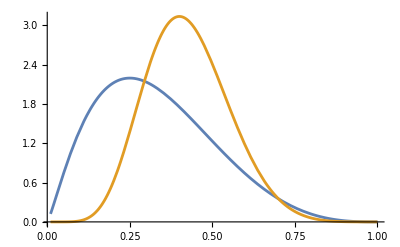

```mathematica
(* BI, beta, and mu defined for plotting distributions *)
ClearAll[w, BI,β,μ ,DI,γ0,BI]
γ0Values=Subdivide[4,16,3];
BI=0.25;
β=.1;
μ = 0.01;


px01=Plot[Evaluate[Table[Pχ0[x,.5,gam*μ],{gam,γ0Values}]],{x,0.05,1},PlotRange->All,PlotStyle->Table[Directive[ColorData["GrayTones"][i/Length[γ0Values]]],{i,1,Length[γ0Values]}]];
px02 =Plot[Evaluate[Table[Pχ0[x,1.5,gam*μ],{gam,γ0Values}]],{x,0.05,1},PlotRange->All,PlotStyle->Table[Directive[ColorData["GrayTones"][i/Length[γ0Values]]],{i,1,Length[γ0Values]}]];
px1=Plot[Evaluate[Table[Pχ[x,gam*(1-μ),β,ϑ[gam*(1-μ),β,.5,BI,gam*μ],.5,BI,gam*μ],{gam,γ0Values}]],{x,0,1},PlotStyle->Table[Directive[ColorData["GrayTones"][i/Length[γ0Values]]],{i,1,Length[γ0Values]}]];
px2 =Plot[Evaluate[Table[Pχ[x,gam*(1-μ),β,ϑ[gam*(1-μ),β,1.5,BI,gam*μ],1.5,BI,gam*μ],{gam,γ0Values}]],{x,0,1},PlotStyle->Table[Directive[ColorData["GrayTones"][i/Length[γ0Values]]],{i,1,Length[γ0Values]}]];
```

```mathematica
(*Font and text boxes*)

FontSize1=12;
Texta=Graphics[{Text[Style["D_I = 0.5",14,Bold,Background->None],Scaled[{.9,0.9}],{0,0},{1,0}]}];
Textb=Graphics[{Text[Style["D_I = 1.5",14,Bold,Background->None],Scaled[{.9,0.9}],{0,0},{1,0}]}];
Textc=Graphics[{Text[Style["D_I = 0.5",14,Bold,Background->None],Scaled[{.9,0.9}],{0,0},{1,0}]}];
Textd=Graphics[{Text[Style["D_I = 1.5",14,Bold,Background->None],Scaled[{.9,0.9}],{0,0},{1,0}]}];
Texte=Graphics[{Text[Style["γ̄ = 16",14,Background->None],Scaled[{.5,0.8}],{0,0},{1,0}]}];
Textf=Graphics[{Text[Style["γ̄ = 4",14,Background->None],Scaled[{.07,0.4}],{0,0},{1,0}]}];
Textg=Graphics[{Text[Style["γ̄ = 16",14,Background->None],Scaled[{.68,0.75}],{0,0},{1,0}]}];
Texth=Graphics[{Text[Style["γ̄ = 4",14,Background->None],Scaled[{.3,0.3}],{0,0},{1,0}]}];
Texti=Graphics[{Text[Style["γ̄ = 16",14,Background->None],Scaled[{.3,0.4}],{0,0},{1,0}]}];
Textj=Graphics[{Text[Style["γ̄ = 4",14,Background->None],Scaled[{.1,0.1}],{0,0},{1,0}]}];
Textk=Graphics[{Text[Style["γ̄ = 16",14,Background->None],Scaled[{.3,0.35}],{0,0},{1,0}]}];
Textl=Graphics[{Text[Style["γ̄ = 4",14,Background->None],Scaled[{.08,0.08}],{0,0},{1,0}]}];
Textm=Graphics[{Text[Style["",10,Background->None,FontSize1,Bold],{.05,.1},{0,0},{1,0}]}];
Textn=Graphics[{Text[Style["",10,Background->None,FontSize1,Bold],{.05,.1},{0,0},{1,0}]}];
Texto=Graphics[{Text[Style["",10,Background->None,FontSize1,Bold],{.05,4.7},{0,0},{1,0}]}];
Textp=Graphics[{Text[Style["",10,Background->None,FontSize1,Bold],{.05,4.1},{0,0},{1,0}]}];


part1=Show[{px01,Texta,Texti,Textj,Textm},PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_((χ̄)_0)((χ̄)_0)",""},{"(χ̄)_0",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[14,Bold]];
part2=Show[{px02,Textb,Textk,Textl,Textn},PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_((χ̄)_0)((χ̄)_0)",""},{"(χ̄)_0",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[14,Bold]];
part3=Show[{px1,Textc,Textg,Texth,Texto},PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_((χ̄)_1)((χ̄)_1)",""},{"(χ̄)_1",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[14,Bold]];
part4=Show[{px2,Textd,Texte,Textf,Textp},PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_((χ̄)_1)((χ̄)_1)",""},{"(χ̄)_1",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[14,Bold]];
```

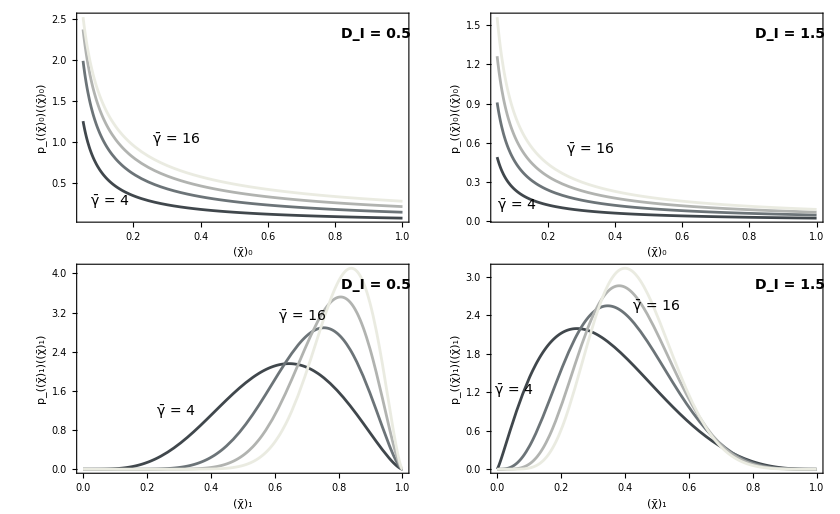

Figure3.pdf

```mathematica
output=Show[GraphicsGrid[{{part1,part2},{part3,part4}},Spacings->{-10,-10}],ImageSize->840]
Export["Figure3.pdf",output]
```

```mathematica
(*Clear variables changed*)
ClearAll[w, BI,β,μ ,DI,γ0,BI]
```

### Figure 5 - CN with Ensemble Average Antecedent Moisture (<S>)

```mathematica
(*Choose range of values for dynamic params*)

(*w is in mm*)
wValues={300,500,1000,2000};
uValues={0.01,0.05,0.1,0.2};
BIValues={0.01,0.4,1,2};

(*default params*)
w =461;
BI=.25;
β=.1;
μ = 0.01;
γ0  = 25;


(*Plot CN_<S> for range of dryness indices, with mu varying*)
```

```mathematica
p1=Plot[Table[CNavg[DI,γ0 *(1-uVal),β,ϑ[γ0 *(1-uVal),β,DI,BI,γ0 *uVal],BI,γ0 *(uVal),w,uVal],{uVal,uValues}],{DI,0.05,2.5},PlotStyle->Directive[Thick,GrayLevel[0.2]],ImagePadding->50,Frame->{True},PlotRangeClipping->False,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},Frame->True,FrameLabel->{DisplayForm[SubscriptBox["D","I"]],DisplayForm[SubscriptBox["CN",StyleBox["⟨ (S̄)_1⟩",Italic]]]},BaseStyle->{14,SingleLetterItalics->True},LabelStyle->Directive[14,Bold,Black],ImageSize->{420},Epilog->{Text[Style["μ = 0.2",12,Background->None,Bold],Scaled[{0.29,0.8}]],Text[Style["μ = 0.01",12,Background->None,Bold],Scaled[{.1,0.7}]]}];
```

```mathematica
(*Plot mu_I for range of dryness indices, with mu varying*)
```

```mathematica
p2=Plot[Table[IS[w,DI,u,γ0*(1-u),ϑ[γ0 *(1-u),β,DI,BI,γ0 *u],γ0*u,BI,β],{u,uValues}],{DI,0.05,2.5},PlotStyle->Directive[Thick,GrayLevel[0.2],Dashed],ImagePadding->50,Frame->{True},PlotRangeClipping->False,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"μ_I",""},{"D_I",""}},LabelStyle->Directive[14,Bold,Black],ImageSize->{420},Epilog->{Text[Style["μ = 0.2",12,Background->None,Bold],Scaled[{0.5,0.45}]],Text[Style["μ = 0.05",12,Background->None,Bold],Scaled[{.15,0.1}]]}];
```

```mathematica
(*Plot CN_<S> for range of dryness indices, with w varying, (461/25 represents base alpha (mm) )*)
```

```mathematica
p3=Plot[Table[CNavg[DI,w/(461/25)*(1-μ),β,ϑ[w/(461/25) *(1-μ),β,DI,BI,w/(461/25) *μ],BI,w/(461/25) *(μ),w,μ],{w,wValues}],{DI,0.05,2.5},PlotStyle->Directive[Thick,GrayLevel[0.2]],ImagePadding->55,Frame->{True},PlotRangeClipping->False,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{DisplayForm[SubscriptBox["D","I"]],DisplayForm[SubscriptBox["CN",StyleBox["⟨ (S̄)_1⟩",Italic]]]},LabelStyle->Directive[14,Bold,Black],ImageSize->{420},Epilog->{Text[Style["w̄ = 2000 mm",12,Background->None,Bold],Scaled[{0.2,0.2}]],Text[Style["w̄ = 300 mm",12,Background->None,Bold],Scaled[{.66,0.66}]]}];
```

```mathematica
(*Plot mu_I for range of dryness indices, with w varying, (461/25 represents base alpha (mm) )*)
```

```mathematica
p4=Plot[Table[IS[w,DI,μ,w/(461/25)*(1-μ),ϑ[w/(461/25) *(1-μ),β,DI,BI,w/(461/25) *μ],w/(461/25) *μ,BI,β],{w,wValues}],{DI,0.05,2.5},PlotStyle->Directive[Thick,GrayLevel[0.2],Dashed],ImagePadding->50,Frame->{True},PlotRangeClipping->False,PlotRange->All,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"μ_I",""},{"DI",""}},LabelStyle->Directive[14,Bold,Black],ImageSize->{420},Epilog->{Text[Style["w̄ = 300 mm",12,Background->None,Bold],Scaled[{0.15,0.1}]],Text[Style["w̄ = 2000 mm",12,Background->None,Bold],Scaled[{.35,0.5}]]}];
```

```mathematica
(*Plot CN_<S> for range of dryness indices, with BI varying, (461/25 represents base alpha (mm) )*)


p5=Plot[Table[CNavg[DI,γ0 *(1-μ),β,ϑ[γ0 *(1-μ),β,DI,BI,γ0 *μ],BI,γ0 *(μ),w,μ],{BI,BIValues}],{DI,0.05,2.5},PlotStyle->Directive[Thick,GrayLevel[0.2]],ImagePadding->50,Frame->{True},PlotRangeClipping->False,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{DisplayForm[SubscriptBox["D","I"]],DisplayForm[SubscriptBox["CN",StyleBox["⟨ (S̄)_1⟩",Italic]]]},LabelStyle->Directive[14,Bold,Black],ImageSize->{420},Epilog->{Text[Style["B_I= 0.01",12,Background->None,Bold],Scaled[{0.5,0.5}]],Text[Style["B_I = 2",12,Background->None,Bold],Scaled[{.2,0.06}]]}];

(*Plot mu_I for range of dryness indices, with BI varying, (461/25 represents base alpha (mm) )*)

p6=Plot[Table[IS[w,DI,μ,γ0*(1-μ),ϑ[γ0 *(1-μ),β,DI,BI,γ0 *μ],γ0*μ,BI,β],{BI,BIValues}],{DI,0.05,2.5},PlotStyle->Directive[Thick,GrayLevel[0.2],Dashed],ImagePadding->40,Frame->{True},PlotRangeClipping->False,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"μ_I",""},{"D_I",""}},LabelStyle->Directive[14,Bold,Black],ImageSize->{420},Epilog->{Text[Style["B_I = 0.01",12,Background->None,Bold],Scaled[{0.35,0.4}]],Text[Style["B_I = 2",12,Background->None,Bold],Scaled[{.7,0.025}]]},PlotRange->{0,.2}];
```

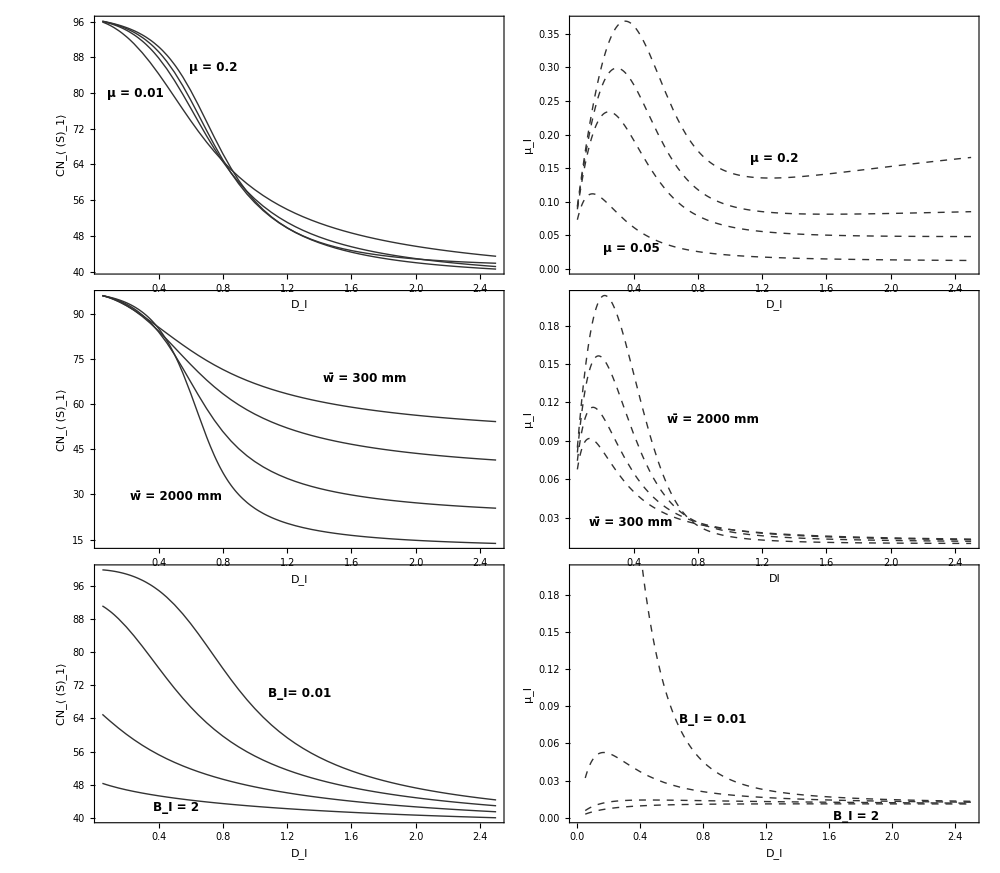

```mathematica
output2=Show[GraphicsGrid[{{p1,p2},{p3,p4},{p5,p6}},Spacings->{-40,-40}],ImageSize->1000]
Export["Figure5.pdf",output2]
```

### Budyko Curve (Figure 7)

```mathematica
(*Plotting Budyko Curves, given by Eq. 30*)
```

```mathematica
ClearAll[w, BI,β,μ ,DI,γ0,BI]

BudykoCurve1 = Table[{DI,DI χ0avgN[DI,γ0* μ]+ DI wPET[DI,γ0*μ] χavg[DI,γ0*(1-μ),β,ϑ[γ0 *(1-μ),β,DI,BI,γ0 *μ],BI,γ0*μ]}/.{γ0->20,BI->.1, μ->.01},{β,{.01,0.9}},{DI,.05,3,.01}];

BudykoCurve2 = Table[{DI,DI  χ0avgN[DI,γ0* μ]+ DI  wPET[DI,γ0*μ] χavg[DI,γ0*(1-μ),β,ϑ[γ0 *(1-μ),β,DI,BI,γ0 *μ],BI,μ*γ0]}/.{γ0->20,β->.1, μ->.01},{BI,{0.01,.3,.9,2,4}},{DI,.05,3,.01}];

BudykoCurve3 = Table[{DI,DI  χ0avgN[DI,γ0* μ]+ DI  wPET[DI,γ0*μ] χavg[DI,γ0*(1-μ),β,ϑ[γ0 *(1-μ),β,DI,BI,γ0 *μ],BI,μ*γ0]}/.{γ0->20,β->.1, BI->.1},{μ,{0.01,.07,.2}},{DI,.05,3,.01}];

BudykoCurve4 = Table[{DI,DI  χ0avgN[DI,γ0* μ]+ DI  wPET[DI,γ0*μ] χavg[DI,γ0*(1-μ),β,ϑ[γ0 *(1-μ),β,DI,BI,γ0 *μ],BI,μ*γ0]}/.{β->.1,BI->.1, μ->.01},{γ0,{2,4,10,38,80}},{DI,.05,3,.01}];

BudykoCurveMatch = Table[{DI,DI χ0avgN[DI,γ0* μ]+ DI  wPET[DI,γ0*μ] χavg[DI,γ0*(1-μ),β,ϑ[γ0 *(1-μ),β,DI,BI,γ0 *μ],BI,μ*γ0]}/.{γ0->53,β->.9,BI->.7, μ->.05},{DI,.05,3,.01}];
```

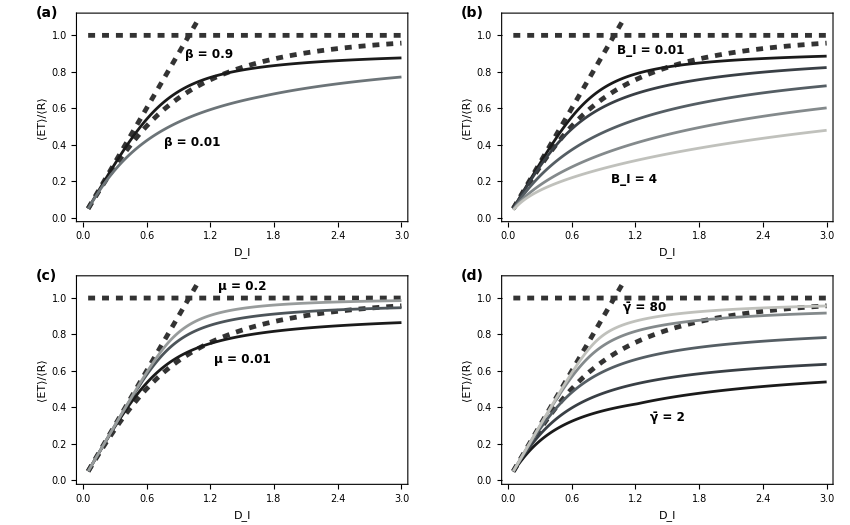

```mathematica
(*Plot functions*)

labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.09,1}]]}]] ;


labeledPlot[Show[pt11,ListPlot[BudykoCurveMatch,Joined->True ],ImageSize->Medium],"a"];


Budyko[DI_]:=(DI(1-ⅇ^-DI)Tanh[1/DI])^(.5);

pt11=Plot[{Budyko[DI],1,DI},{DI,0.05,3},PlotRange->{0,1.1},Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"\!\(\*
StyleBox[\"⟨\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"ET\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"⟩\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"/\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"⟨\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"R\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"⟩\",\nFontSlant->\"Italic\"]\)",""},{"\!\(\*SubscriptBox[\(D\), \(I\)]\)",""}},PlotStyle->{{Thickness[.006],GrayLevel[.2],Dashed}},LabelStyle->Directive[14,Bold],PlotRangeClipping->False];

FigAppendix1=Show[pt11,ListPlot[BudykoCurve1,Joined->True ],ImageSize->Medium];
FigAppendix2=Show[pt11,ListPlot[BudykoCurve2,Joined->True ],ImageSize->Medium];
FigAppendix3=Show[pt11,ListPlot[BudykoCurve3,Joined->True ],ImageSize->Medium];
FigAppendix4=Show[pt11,ListPlot[BudykoCurve4,Joined->True ],ImageSize->Medium];
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.09,1}]]}]]
generateColors[data_]:=ColorData["GrayTones"]/@Rescale[Range[Length[data]+1]];

FigAppendix1=labeledPlot[Show[pt11,ListPlot[BudykoCurve1,Joined->True,PlotStyle->(generateColors[BudykoCurve1])],ImageSize->Large,Epilog->{Text[Style["β = 0.01",12,Background->None,Bold],Scaled[{0.35,0.38}]],Text[Style["β = 0.9",12,Background->None,Bold],Scaled[{.4,0.8}]]}],"(a)"];

FigAppendix2=labeledPlot[Show[pt11,ListPlot[BudykoCurve2,Joined->True,PlotStyle->(generateColors[BudykoCurve2])],ImageSize->Large,Epilog->{Text[Style["B_I = 4",12,Background->None,Bold],Scaled[{0.4,0.2}]],Text[Style["B_I = 0.01",12,Background->None,Bold],Scaled[{.45,0.82}]]}],"(b)"];

FigAppendix3=labeledPlot[Show[pt11,ListPlot[BudykoCurve3,Joined->True,PlotStyle->(generateColors[BudykoCurve3])],ImageSize->Large,Epilog->{Text[Style["μ = 0.2",12,Background->None,Bold],Scaled[{0.5,0.95}]],Text[Style["μ = 0.01",12,Background->None,Bold],Scaled[{.5,0.6}]]}],"(c)"];

FigAppendix4=labeledPlot[Show[pt11,ListPlot[BudykoCurve4,Joined->True,PlotStyle->(generateColors[BudykoCurve4])],ImageSize->Large,Epilog->{Text[Style["γ̄ = 80",12,Background->None,Bold],Scaled[{0.43,0.85}]],Text[Style["γ̄ = 2",12,Background->None,Bold],Scaled[{.5,0.32}]]}],"(d)"];

BudykoFinal = GraphicsGrid[{{FigAppendix1,FigAppendix2},{FigAppendix3,FigAppendix4}},Spacings->0.5,ImageSize->850]
```

```mathematica
Export["Figure7.pdf",BudykoFinal]
```

Figure7.pdf

### CN Statistics Plot (Figure 6)

```mathematica
ClearAll[w, BI,β,μ ,DI,γ0,BI]
MinCN = 25400./(w(1-μ)(1-0)+254)/.{w->461, μ->0.05, β->.9,BI->.7, α->w/53};

(*Listing 25 and 75% quantiles for ET*)
Part2=Plot[Evaluate[{DI*χ0avg[DI,γ0*μ]+DI*wPET[DI,γ0*μ]*Qχ[.25,DI,γ0,β,μ,BI],DI*χ0avg[DI,γ0*μ]+DI*wPET[DI,γ0*μ]*Qχ[0.75,DI,γ0,β,μ,BI]}/. {γ0->53,μ->0.05,BI->0.7,β->0.9}],{DI,0.1,2.5},PlotStyle->{{Dashed,GrayLevel[.1]},{Dashed,GrayLevel[.1]}},Filling->{1->{2}}];
```

```mathematica
(*Listing 25 and 75% quantiles for ET*)
QET25list2 = Table[{DI,1/Rf[DI] QcET2[.25,DI,γ0,β,μ,BI,DI Rf[DI]]/.{γ0->53,μ->0.05,BI->0.7,β->0.9}},{DI,0.1,2.5,0.1}]
QET75list2 = Table[{DI,1/Rf[DI] QcET2[.75,DI,γ0,β,μ,BI,DI Rf[DI]]/.{γ0->53,μ->0.05,BI->0.7,β->0.9}},{DI,0.1,2.5,0.1}]
Part1=Plot[{Budyko[DI],DI UnitStep[1-DI]+1-UnitStep[1-DI]},{DI,0.1,2.5}, PlotStyle->{{ GrayLevel[.2]}}];
Part22 = ListPlot[{QET25list2,QET75list2 },Joined->True,PlotStyle->{{Dashed,GrayLevel[.7]},{Dashed,GrayLevel[.7]}},Filling->{1->{2}}];
```

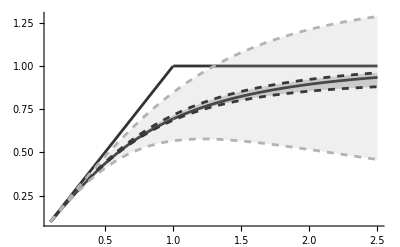

```mathematica
Show[Part1,Part2,Part22,PlotRange->All]
```

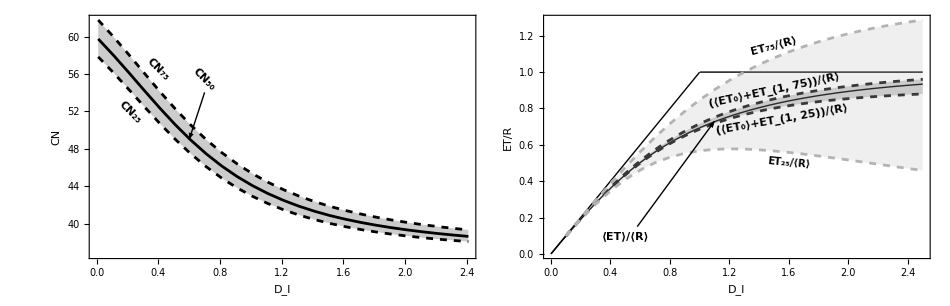

Figure6.pdf

```mathematica
Part1=Plot[{Budyko[DI],DI UnitStep[1-DI]+1-UnitStep[1-DI]},{DI,0,2.5},PlotStyle->{{Thick,GrayLevel[.01]}},(*Only gray color applied here*)Frame->True,FrameStyle->{{Directive[Black],Transparent},{Directive[Black],Transparent}},FrameLabel->{{"\!\(\*FractionBox[StyleBox[\"ET\", FontSlant->\"Italic\"], \(R\)]\)",""},{"\!\(\*SubscriptBox[\(D\), \(I\)]\)",""}},LabelStyle->Directive[14,Bold],Epilog->{Text[Rotate[Style["\!\(\*SubscriptBox[StyleBox[\"ET\", FontSlant->\"Italic\"], \(75\)]\)/⟨R⟩",Bold,11],15 Degree],{1.5,1.15}],Text[Rotate[Style["\!\(\*SubscriptBox[StyleBox[\"ET\", FontSlant->\"Italic\"], \(25\)]\)/⟨R⟩",Bold,10],-5 Degree],{1.6,.5}],Text[Rotate[Style["(⟨\!\(\*SubscriptBox[StyleBox[\"ET\", FontSlant->\"Italic\"], \(0\)]\)⟩+\!\(\*SubscriptBox[StyleBox[\"ET\", FontSlant->\"Italic\"], \(1, 75\)]\))/⟨R⟩",Bold,11],12 Degree],{1.5,0.9}],Text[Rotate[Style["(⟨\!\(\*SubscriptBox[StyleBox[\"ET\", FontSlant->\"Italic\"], \(0\)]\)⟩+\!\(\*SubscriptBox[StyleBox[\"ET\", FontSlant->\"Italic\"], \(1, 25\)]\))/⟨R⟩",Bold,11],10 Degree],{1.55,.74}],Text[Rotate[Style["⟨\!\(\*StyleBox[\"ET\", FontSlant->\"Italic\"]\)⟩/⟨R⟩",Bold,11],0 Degree],{.5,.1}],Arrowheads[0.025],(*Smaller arrowhead*)Arrow[{{.58,0.15},{1.1,0.73}}]}];



highTab = Table[{DI, QCN[.75,w,μ,α,BI,DI,β]}/.{w->46.1*10, μ->0.05, β->.9,BI->.7, α->8.7},{DI,.01,2.5,.1}];
medTab = Table[{DI, QCN[.5,w,μ,α,BI,DI,β]}/.{w->46.1*10, μ->0.05, β->.9,BI->.7, α->8.7},{DI,.01,2.5,.1}];
lowTab = Table[{DI, QCN[.25,w,μ,α,BI,DI,β]}/.{w->46.1*10, μ->0.05, β->.9,BI->.7, α->8.7},{DI,.01,2.5,.1}];


aa=ListPlot[{lowTab,medTab,highTab},Joined->True,PlotRange->All,PlotStyle->{{Black,Dashed},{Black},{Black,Dashed}},Filling->{{1->{3}}},AxesLabel->{"DI","Quantile Value"},Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"CN",""},{"D_I",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[14,Bold],Epilog->{Text[Rotate[Style["\!\(\*SubscriptBox[\(CN\), \(75\)]\)",Bold,11],-45 Degree],{.4,56.5}],Text[Rotate[Style["\!\(\*SubscriptBox[\(CN\), \(25\)]\)",Bold,11],-45 Degree],{.22,51.9}],Text[Rotate[Style["\!\(\*SubscriptBox[\(CN\), \(50\)]\)",Bold,11],-45 Degree],{.7,55.4}],Arrowheads[0.025],Arrow[{{.7,54.04},{.6,49}}]}];


output6=Show[GraphicsGrid[{{Show[aa],Show[Part1,Part2,Part22,PlotRange->All]}},Spacings->{-30,0}],ImageSize->950,PlotRangeClipping->False]
Export["Figure6.pdf",output6]
```